```mathematica
SetDirectory[NotebookDirectory[]<>"/../"];
<<SimulationRewardDriven1`;
SetDirectory[NotebookDirectory[]];
(*displays results of simulation*)
PlotBelief1[]:=Table[Mean/@BELIEF[[i]],{i,1,BELIEF//Length}]//ListLinePlot[#,AxesLabel->{Style["j",Large],Style["d",Large]},PlotRange->All,PlotLegends->Table[Style["a= "<>ToString[AffinityValues[[i]]]<>", b="<>ToString[BiasValues[[i]]],Large],{i,1,AffinityValues//Length}],ImageSize->Large,TicksStyle->Directive["Label", 20]]&;
```

Initialize simulation. 
This sets up the INITIAL values for d,a,b,h which are all lists of size ‘nquestionsUSER’:
- d:  is  the degree of belief on the theory (theory is correct by construction)
- a:  the affinity or tendency for experts to change their belief on the theory, motivated by getting higher rewards.
- b:  is the bias or tendency to reject the objective outcome of experiments, based on their own belief of the theory 
- h:  random walk parameter, associated to the  probability  of experts to change their degree of belief randomly,
          Probability of Random Walk = 2h(1-h)
         examples:  h=0.5   →  50%   ,  h=0.99   →  2% ,  h=1.0   →  0% (no random walk).
The simulation performs a number of experiments given by ‘nexperimentsUSER’. Each experiment asks a number of questions given by  ‘nquestionsUSER’

```mathematica
nquestionsUSER=300;
nexperimentsUSER=5;
npredictorsUSER=10;
d=ConstantArray[-2,npredictorsUSER];d[[1]]=2;
a=ConstantArray[5,npredictorsUSER];
b=ConstantArray[0,npredictorsUSER];
h=ConstantArray[0.99,npredictorsUSER];
InitSimulationRewardDriven[d,a,b,h]
```

Run simulation. 
This runs a ‘for-loop’, each iteration corresponds to an experiment. The first iteration uses values set up above for d,a,b,h. 
The degree of belief d is updated according to a,b,h. At the end of every iteration, the values of a,b are changed to be used for the next iteration.
The value of h stays constant during the entire simulation.

```mathematica
For[it=1,it≤nexperimentsUSER,it++,
(*stores values of a,b for all iterations*)
AppendTo[AffinityValues,a//Mean];
AppendTo[BiasValues,b//Mean];
(*to show progress*)
templine=PrintTemporary[Style["it=",Large,Bold],Style[it,Large,Bold]];
(*initialize experiment*)
InitExperimentRewardDriven[d,a,b,h];
(*run experiment*)
RunExperiment[];
(*saves data on degree of belief during the simulation*)
StoreBeliefCurrent[];
(*change values of a,b for next iteration*)
(*a=ConstantArray[RandomReal[{0.1,5}],npredictors];
b=ConstantArray[RandomReal[{5,10}],npredictors];*)
(*deletes display of progress *)
NotebookDelete[templine];
]
```

Plot results
use function ‘PlotBelief1[]’ to see results. Relevant data is stored in the various “superarrays” of ‘EQLab’ and a new one called ‘BELIEF’. After running the initialization step, everything gets wiped out, so please save and organize your progress before running a new simulation.

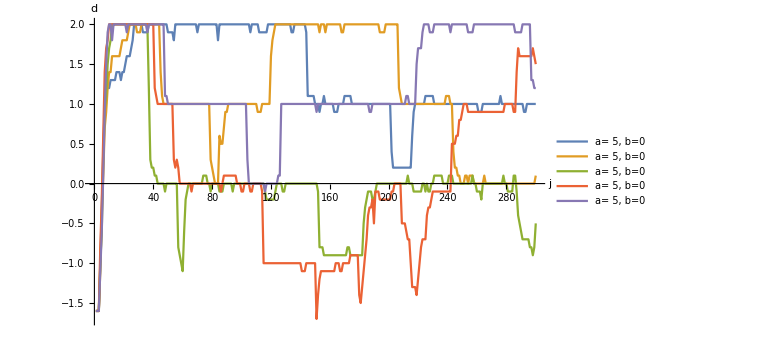

```mathematica
PlotBelief1[]
```

```mathematica
EXPERIMENT[[-1]]
```

{1}
 |  |  |  |

-Graphics-

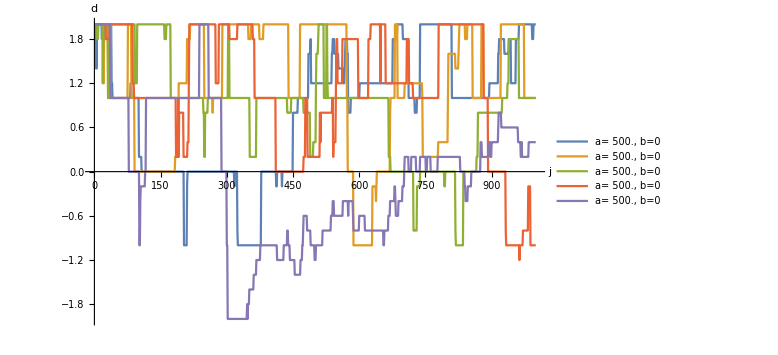

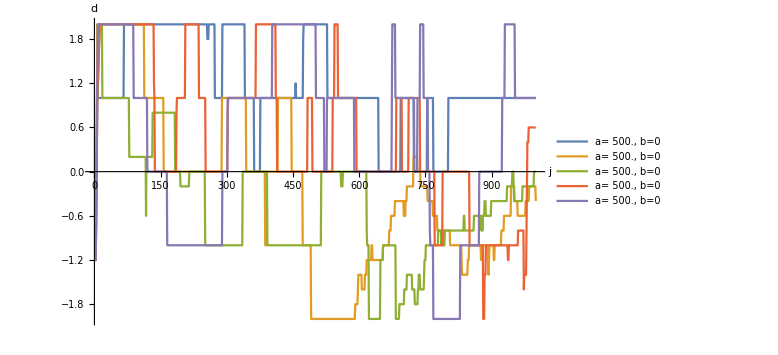

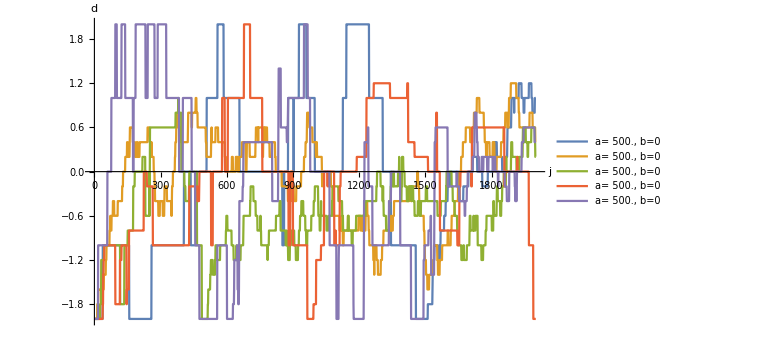

```mathematica
ShowPlots[-1,"r"]
```

## h=0.99, d_init={0,0,0,0,0}

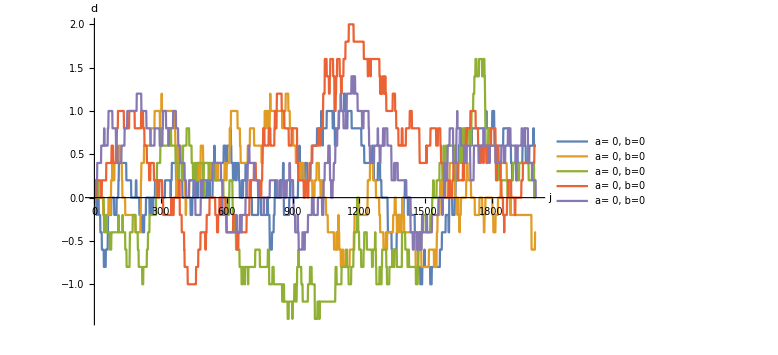

## h=0.99, d_init={2,2,2,2,2}

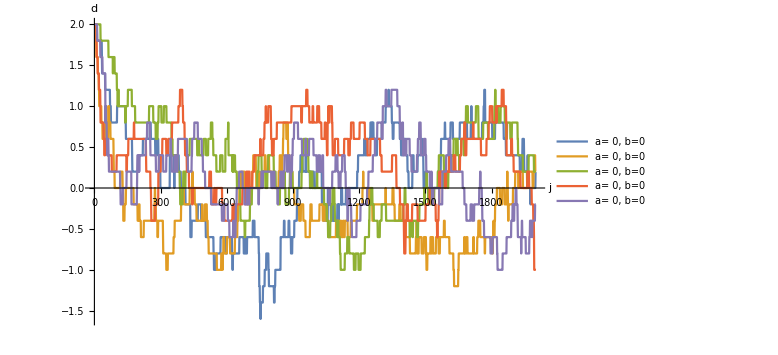

## h=0.99, d_init={-2,-2,-2,-2,-2}

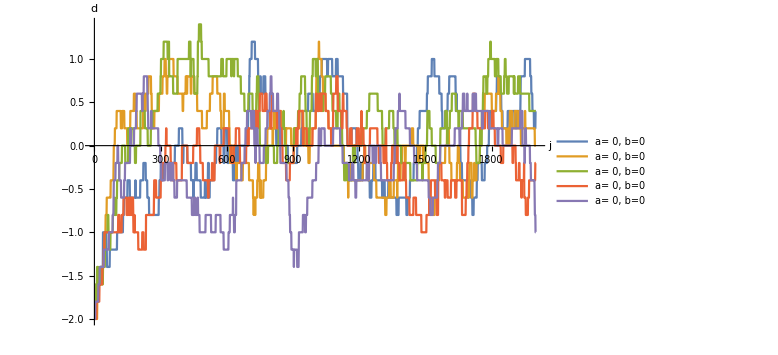

## h=0.99, d_init={-2,-2,-2,-2,-2}

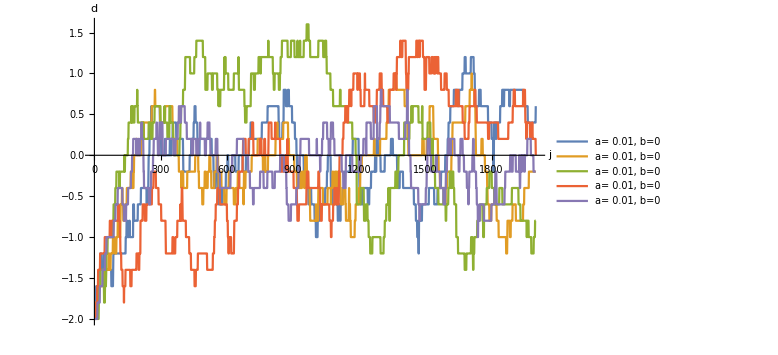

## h=0.99, d_init={-2,-2,-2,-2,-2}

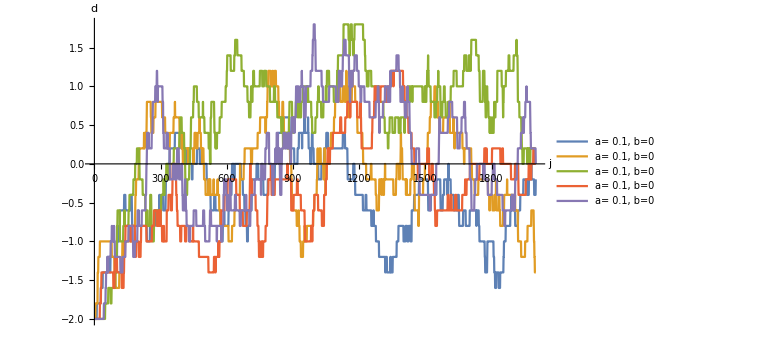

## h=0.99, d_init={-2,-2,-2,-2,-2}

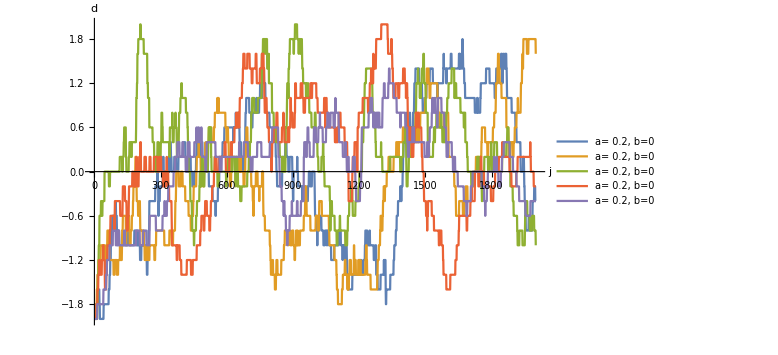

## h=0.99, d_init={-2,-2,-2,-2,-2}

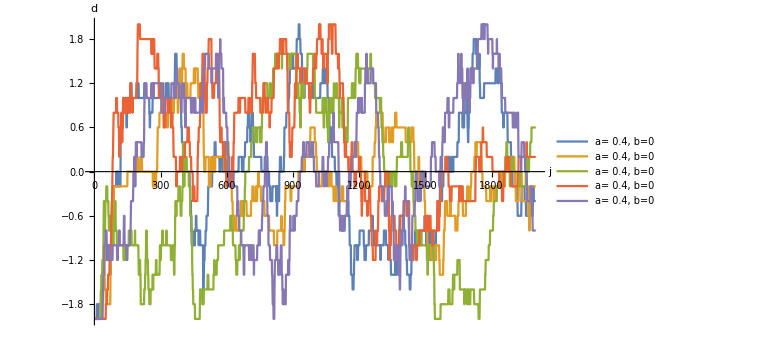

## h=0.99, d_init={-2,-2,-2,-2,-2}

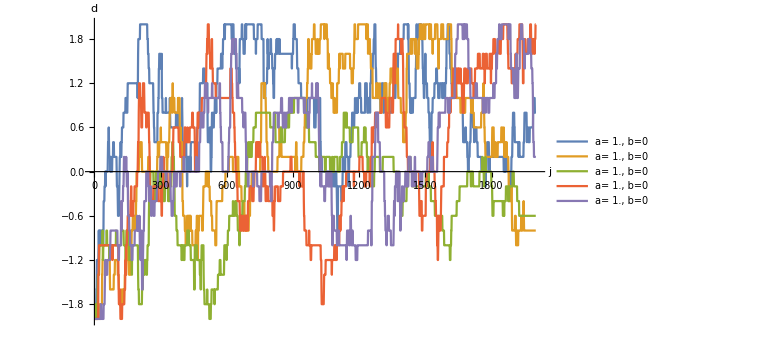

## h=0.99, d_init={-2,-2,-2,-2,-2}

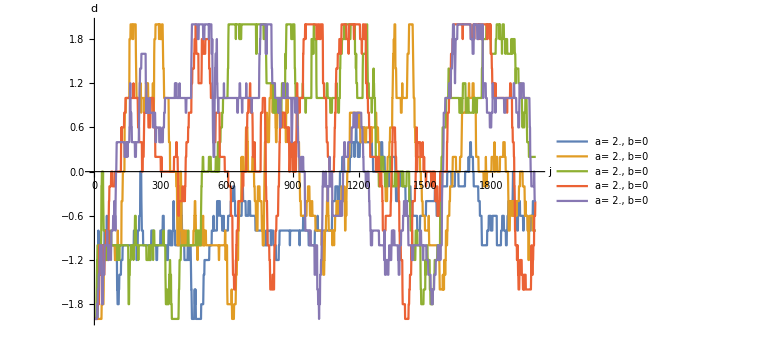

## h=0.99, d_init={-2,-2,-2,-2,-2}

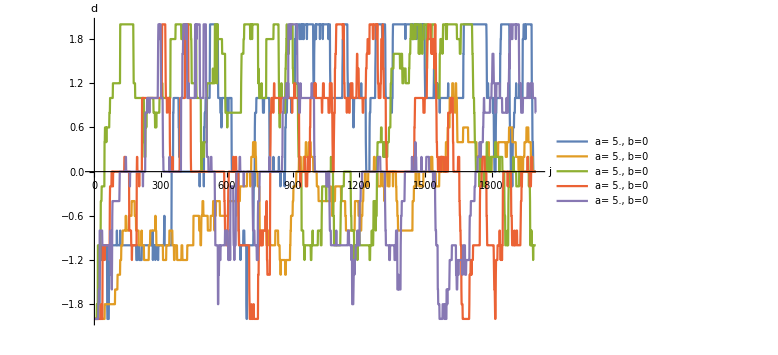

```mathematica
Integrate[2 π kT Exp[-kT^2/m^2],{kT,0,muQ}]//Limit[#,muQ->∞]&
```

ConditionalExpression[m^2 π, (1/m^2|m^2|m)∈ℝ]